```mathematica
Manipulate[
 Module[
  {
   eqns, sol, H, Z, T, R, t, Hfunc, Zfunc, Tfunc, Rfunc, fixedPoints, 
   phasePlotHZ, phasePlotZT, jMatrix, parameterSpace,
   detJ, finalDetJ, traceJ, finalTraceJ
  },
  
  (* Define the differential equations *)
  eqns = {
    H'[t] == - βZ H[t] Z[t],
    Z'[t] == (βZ-δZH) H[t] Z[t] - δZ T[t] Z[t],
    T'[t] == βT R[t] - δT T[t],
    R'[t] ==  δZH H[t] Z[t] + δZ T[t] Z[t] - βT R[t]
  };
  
  jMatrix = {
   {-βZ Z, -βZ H, 0},
   {βZ Z, βZ H - δZ, 0},
   {0, δZ H, 0}
};
  
  parameterSpace = ParametricPlot[{{d,0},{0,t},{t^2/4,t}},{d,-10,10},{t,-10,10},PlotRange->{{-10,10},{-10,10}}];
  
  (* Solve the equations numerically *)
  sol = NDSolve[
    {eqns, 
     H[0] == H0, 
     Z[0] == Z0,
     T[0] == T0,
     R[0] == R0
    }, 
    {H, Z, T, R}, 
    {t, 0, tmax}
  ];
  
  (* Extract solution functions *)
  Hfunc = H /. sol[[1]];
  Zfunc = Z /. sol[[1]];
  Tfunc = T /. sol[[1]];
  Rfunc = R /. sol[[1]];
  
  traceJ = Tr[jMatrix];
  detJ = Det[jMatrix];
  finalTraceJ = traceJ /. {H -> (H[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), βZ -> βZ, δZ -> δZ };
  finalDetJ = detJ /. {H -> (H[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), βZ -> βZ, δZ -> δZ };
  
  
  
  (* Generate phase space stream plot *)
  phasePlotHZ = 
   StreamPlot[
    Evaluate[{
    
      - βZ H Z + δT T, 
      βZ H Z - δZ T Z - δZH H Z
    } /. {T -> Tfunc[tmax]}],
    {H, 0, 1}, {Z, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"H (Humans)", "Z (Zombies)"},
    Frame -> True,
    FrameLabel -> {"H (Humans)", "Z (Zombies)"}
   ];
   phasePlotZT = 
   StreamPlot[
    Evaluate[{ 
      βZ H Z - δZ T Z - δZH H Z,
      βT R - δT T
    } /. {R -> Rfunc[tmax], H -> Hfunc[tmax]}],
    {Z, 0, 1}, {T, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"H (Humans)", "Z (Zombies)"},
    Frame -> True,
    FrameLabel -> {"H (Humans)", "Z (Zombies)"}
   ];
  
  (* Display the results *)
  Column[{
    Plot[
     {Hfunc[t], Zfunc[t], Tfunc[t], Rfunc[t]},
     {t, 0, tmax},
     PlotRange -> All,
     PlotLegends -> {"Humans (S)", "Zombies (Z)", "Turned (T)", "Removed (R)"},
     PlotStyle -> {{Blue, Thick}, {Red, Thick}, {Green, Thick}, {Purple, Thick}},
     AxesLabel -> {"Time (t)", "Population"},
     Frame -> True,
     FrameLabel -> {"Time (t)", "Population Fractions"}
    ],
    phasePlotHZ,
    phasePlotZT
   }]
 ],
 
 (* Sliders for parameters and initial conditions *)
 {{βZ, 0.0095, "Zombification rate S to Z (beta_Z)"}, 0, 1, 0.001},
 {{δZ, 0.013, "Zombie removal rate (delta_Z)"}, 0, 1, 0.001},
 {{δZH, 0.006, "Zombie removal rate by humans (delta_Z)"}, 0, 1, 0.001},
 {{βT, 0.003, "Mutation rate Z to T (beta_T)"}, 0, 1, 0.001},
 {{δT, 0.002, "Turned removal rate (delta_T)"}, 0, 1, 0.001},
 {{H0, 500, "Initial humans (S0)"}, 0.1, 5000, 1},
 {{Z0, 100, "Initial zombies (Z0)"}, 0, 5000, 1},
 {{T0, 100, "Initial turned (T0)"}, 0, 5000, 1},
 {{R0, 0, "Initial removed (R0)"}, 0, 5000, 1},
 {{tmax, 10000, "Simulation time"}, 10, 1000000, 1}
]
```

## Non-Dimensionalisation

```mathematica
Manipulate[
 Module[
  {
   eqns, sol, H, Z, T, R, t, Hfunc, Zfunc, Tfunc, Rfunc, fixedPoints, 
   phasePlotHZ, phasePlotZT, jMatrix, parameterSpace,
   detJ, finalDetJ, traceJ, finalTraceJ
  },
  
  (* Define the differential equations *)
  eqns = {
    H'[t] == -H[t] Z[t] + δT T[t],
    Z'[t] == (1-δZH) H[t] Z[t] - δZ T[t] Z[t],
    T'[t] == βT R[t] - δT T[t],
    R'[t] ==  δZH H[t] Z[t] + δZ T[t] Z[t] - βT R[t]
  };
  
  jMatrix = {
   {- Z, - H, δT, 0},
   {(1-δZH)Z, (1-δZH)H - δZ T, - δZ Z, 0},
   {0, 0, - δT, βT},
   {δZH Z, δZH H + δZ T, δZ Z, βT}
};
  
  parameterSpace = ParametricPlot[{{d,0},{0,t},{t^2/4,t}},{d,-10,10},{t,-10,10},PlotRange->{{-1,1},{-1,1}}];
  
  (* Solve the equations numerically *)
  sol = NDSolve[
    {eqns, 
     H[0] == H0/H0, 
     Z[0] == Z0/H0,
     T[0] == T0/H0,
     R[0] == R0/H0
    }, 
    {H, Z, T, R}, 
    {t, 0, tmax}
  ];
  
  (* Extract solution functions *)
  Hfunc = H /. sol[[1]];
  Zfunc = Z /. sol[[1]];
  Tfunc = T /. sol[[1]];
  Rfunc = R /. sol[[1]];
  
  traceJ = Tr[jMatrix];
  detJ = Det[jMatrix];
  finalTraceJ = traceJ /. {H -> (H[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), T -> (T[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), δZ -> δZ };
  finalDetJ = detJ /. {H -> (H[tmax] /. sol[[1]]), Z -> (Z[tmax] /. sol[[1]]), T -> (T[tmax] /. sol[[1]]), R -> (R[tmax] /. sol[[1]]), δZ -> δZ };
  
  
  
  (* Generate phase space stream plot *)
  phasePlotHZ = 
   StreamPlot[
    Evaluate[{
    
      - H Z + δT T, 
      (1-δZH) H Z - δZ T Z
    } /. {T -> Tfunc[tmax]}],
    {H, 0, 1}, {Z, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"H (Humans)", "Z (Zombies)"},
    Frame -> True,
    FrameLabel -> {"H (Humans)", "Z (Zombies)"}
   ];
   phasePlotZT = 
   StreamPlot[
    Evaluate[{ 
      (1-δZH) H Z - δZ T Z,
      βT R - δT T
    } /. {R -> Rfunc[tmax], H -> Hfunc[tmax]}],
    {Z, 0, 1}, {T, 0, 1},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    AxesLabel -> {"Z (Zombies)", "T (Turned)"},
    Frame -> True,
    FrameLabel -> {"Z (Zombies)", "T (Turned)"}
   ];
  
  (* Display the results *)
  Column[{
    Plot[
     {Hfunc[t], Zfunc[t], Tfunc[t], Rfunc[t]},
     {t, 0, tmax},
     PlotRange -> All,
     PlotLegends -> {"Humans (S)", "Zombies (Z)", "Turned (T)", "Removed (R)"},
     PlotStyle -> {{Blue, Thick}, {Red, Thick}, {Green, Thick}, {Purple, Thick}},
     AxesLabel -> {"Time (t)", "Population"},
     Frame -> True,
     FrameLabel -> {"Time (t)", "Population Fractions"}
    ],
    phasePlotHZ,
    phasePlotZT,
    Show[
		parameterSpace,
		ListPlot[{{finalDetJ,finalTraceJ}},PlotStyle->PointSize[Large]]
	]
   }]
 ],
 
 (* Sliders for parameters and initial conditions *)
 {{δZ, 1.36, "Zombie removal rate (delta_Z)"}, 0, 2, 0.001},
 {{δZH, 0.632, "Zombie removal rate by humans (delta_Z)"}, 0, 2, 0.001},
 {{βT, 0.31, "Mutation rate Z to T (beta_T)"}, 0, 2, 0.001},
 {{δT, 0.2, "Turned removal rate (delta_T)"}, 0, 2, 0.001},
 {{H0, 500, "Initial humans (S0)"}, 0.1, 5000, 1},
 {{Z0, 100, "Initial zombies (Z0)"}, 0, 5000, 1},
 {{T0, 100, "Initial turned (T0)"}, 0, 5000, 1},
 {{R0, 0, "Initial removed (R0)"}, 0, 5000, 1},
 {{tmax, 10000, "Simulation time"}, 10, 1000000, 1}
]
```

```mathematica
jMatrix = {
   {- Z, - H, δT, 0},
   {(1-δZH)Z, (1-δZH)H - δZ T, - δZ Z, 0},
   {0, 0, - δT, βT},
   {δZH Z, δZH H + δZ T, δZ Z, βT}
};

fixedPoint1 = {Z -> 0};
fixedPoint2 = {H -> 0};
fixedPoint3 = {H -> 0, Z -> 0, T -> 0, R -> 0};

genEigenVals = Eigenvalues[jMatrix];
eigenVals1 = Eigenvalues[jMatrix /. fixedPoint1];
eigenVals2 = Eigenvalues[jMatrix /. fixedPoint2];
eigenVals3 = Eigenvalues[jMatrix /. fixedPoint3];
```

InterpolatingFunction::dmval: Input value {2000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

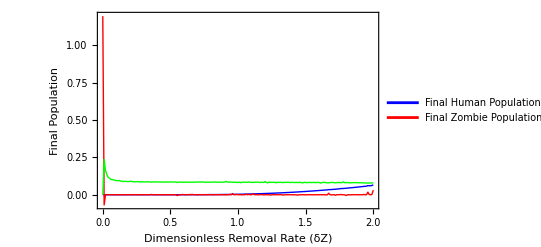

```mathematica
(* Compute final values of H and Z for varying deltaZ *)
finalValues = Table[
  Module[
    {sol, Hfunc, Zfunc, Tfunc, finalH, finalZ, finalT},
    (* Define the differential equations *)
    eqns = {
    H'[t] == -H[t] Z[t],
    Z'[t] == (1-δZH) H[t] Z[t] - δZ T[t] Z[t],
    T'[t] == βT R[t] - δT T[t],
    R'[t] ==  δZH H[t] Z[t] + δZ T[t] Z[t] - βT R[t]
  };
    
    (* Solve the system numerically for the current deltaZ *)
    sol = NDSolve[
      {eqns /. {δZH -> 0.006, δT -> 0.002, βT -> 0.003}, 
       H[0] == 500/500, 
       Z[0] == 100/500,
       T[0] == 100/500,
       R[0] == 0/500
      },
      {H, Z, T, R}, 
      {t, 0, 1200}
    ];
    
    (* Extract the functions for H and Z *)
    Hfunc = H /. sol[[1]];
    Zfunc = Z /. sol[[1]];
    Tfunc = T /. sol[[1]];
    
    (* Extract the final values of H and Z at time tmax *)
    finalH = Hfunc[2000];
    finalZ = Zfunc[2000];
    finalT = Tfunc[2000];
    
    (* Return the deltaZ and final values for plotting *)
    {δZ, finalH, finalZ, finalT}
  ],
  {δZ, 0, 2, 0.01} (* Vary deltaZ from 0 to 2 in steps of 0.01 *)
];

(* Separate deltaZ, H, and Z values for plotting *)
deltaZValues = finalValues[[All, 1]];
finalHValues = finalValues[[All, 2]];
finalZValues = finalValues[[All, 3]];
finalTValues = finalValues[[All, 4]];

(* Plot final human and zombie populations as a function of deltaZ *)
ListLinePlot[
  {
   Transpose[{deltaZValues, finalHValues}],
   Transpose[{deltaZValues, finalZValues}],
   Transpose[{deltaZValues, finalTValues}]
  },
  PlotRange -> All,
  PlotLegends -> {"Final Human Population (H)", "Final Zombie Population (Z)"},
  PlotStyle -> {{Blue, Thick}, {Red, Thick}, {Green, Thick}},
  AxesLabel -> {"Zombie Removal Rate (δZ)", "Final Population"},
  Frame -> True,
  FrameLabel -> {"Dimensionless Removal Rate (δZ)", "Final Population"}
]
```